# SHiP Detector

Run this first

### Defining ellipse geometry and functions for computing event yield

In the form x,y,z (of the first cap centre), length, horizontal semi-axis (y), vertical semi-axis (x), and detector angle. All in m. x is up, y is to the right, and z is down the beampipe. The detector angle ranges from -π/2 - π/2 and is defined as the angle between a line running parallel to the detector length and the beamline in the x-z plane.

```mathematica
ellipseDef ={0,0, 68.8,55,5,2.5,0}
```

{0,0,68.8,55,5,2.5,0}

#### Setting up cylinder definitions and relevant coordinate transformations

```mathematica
θfromη[η_]:=2 ArcCot[ⅇ^η];
ηfromθ[θ_]:=-Log[Tan[θ/2]];
```

Creates a parametric definition f(r,α) (caps) and f(l,α) (body). α runs from 0 to 2π and r from 0 to 1

```mathematica
planeSegmentsFromEllipse[ellipseDef_]:={
{Cos[ellipseDef[[7]]](ellipseDef[[6]]*r*Sin[α])+ellipseDef[[1]],ellipseDef[[2]]+ellipseDef[[5]]*r*Cos[α],ellipseDef[[3]]-Sin[ellipseDef[[7]]](ellipseDef[[6]]*r*Sin[α])}
,
{ellipseDef[[1]]+Cos[ellipseDef[[7]]](ellipseDef[[6]]*r*Sin[α])+Sin[ellipseDef[[7]]]*ellipseDef[[4]],ellipseDef[[2]]+ellipseDef[[5]]*r*Cos[α],ellipseDef[[3]]+Cos[ellipseDef[[7]]]ellipseDef[[4]]-Sin[ellipseDef[[7]]](ellipseDef[[6]]*r*Sin[α])}
,
{ellipseDef[[1]] +Cos[ellipseDef[[7]]](ellipseDef[[6]]*Sin[α])+Sin[ellipseDef[[7]]](r*ellipseDef[[4]]),ellipseDef[[2]]+ellipseDef[[5]]*Cos[α],ellipseDef[[3]]+Cos[ellipseDef[[7]]]*(r*ellipseDef[[4]])-Sin[ellipseDef[[7]]]*(ellipseDef[[6]]*Sin[α])}
}
```

```mathematica
(*This sets the trajectory of the particle of interest that originates at the interaction point*)
{lineθ,lineϕ}={0.00,0.};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]}
```

{0.,0.,1. s}

```mathematica
Show[
ParametricPlot3D[{
Evaluate[planeSegmentsFromEllipse[ellipseDef]]
},{r,0,1},{α,0,2Pi},
PlotRange->{{-1,1},{-1,1},{0,11}}12,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[currentline,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"}]
,
ParametricPlot3D[beamaxis,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},PlotStyle->{Gray}]
,
ListPointPlot3D[ellipseIntersectionPoints,PlotStyle->{Red,PointSize[.02]}]
]
```

-Graphics3D-

```mathematica
intersectionEllipseSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromEllipse[ellipseDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ 1) && (s/.#)≥0 (*&& (α/.#)≥-3.1415*))&]//Quiet

ellipseIntersectionPoints=If[Length[intersectionEllipseSolutions]>0,
tempPoints=Sort[currentline/.intersectionEllipseSolutions,#1.#1<#2.#2&];
If[Length[tempPoints] >2, tempPoints[[2]]=tempPoints[[Length[tempPoints]]]];
tempPoints
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
]

{√(ellipseIntersectionPoints[[1]].ellipseIntersectionPoints[[1]]),√(ellipseIntersectionPoints[[2]].ellipseIntersectionPoints[[2]])}
```

{{s→68.8,r→0.},{s→123.8,r→0.}}

{{0.,0.,68.8},{0.,0.,123.8}}

{68.8,123.8}

## Set up particle path geometry

```mathematica
beamaxis={0,0,0}+s{0,0,1};
```

{0.372026 s,0.115081 s,0.921061 s}

{{s→18.6742,r→0.39327,α→-0.425682},{s→13.0428,r→0.488341,α→1.31795}}

{{4.85225,1.50098,12.0132},{6.94727,2.14904,17.2001}}

{13.0428,18.6742}

3D modeling of surface and ray interactions:

-Graphics3D-

estimate geometric coverage

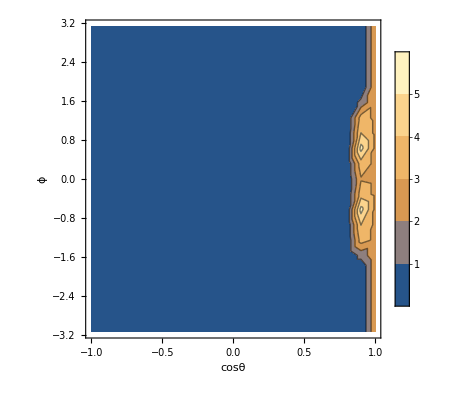

fraction of solid angle covered:

0.05

-Graphics-

```mathematica
(*This sets the trajectory of the particle of interest that originates at the interaction point*)
{lineθ,lineϕ}={0.4,0.3};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]}

(*This determines the intersections of a particle trajectory (currentline) and a detector determined by cylinder dfinition *)
intersectionEllipseSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromEllipse[ellipseDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ 1) && (s/.#)≥0 (*&& (α/.#)≥-3.1415*))&]//Quiet

ellipseIntersectionPoints=If[Length[intersectionEllipseSolutions]>0,
tempPoints=Sort[currentline/.intersectionEllipseSolutions,#1.#1<#2.#2&];
If[Length[tempPoints] >2, tempPoints[[2]]=tempPoints[[Length[tempPoints]]]];
tempPoints
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
]

{√(ellipseIntersectionPoints[[1]].ellipseIntersectionPoints[[1]]),√(ellipseIntersectionPoints[[2]].ellipseIntersectionPoints[[2]])}

"3D modeling of surface and ray interactions:"
Show[
ParametricPlot3D[{
Evaluate[planeSegmentsFromEllipse[ellipseDef]]
},{r,0,1},{α,0,2Pi},
PlotRange->{{-1,1},{-1,1},{-1,2}}12,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[currentline,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"}]
,
ParametricPlot3D[beamaxis,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},PlotStyle->{Gray}]
,
ListPointPlot3D[ellipseIntersectionPoints,PlotStyle->{Red,PointSize[.02]}]
]

"estimate geometric coverage"
L2mL1Ellasfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionEllipseSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromEllipse[ellipseDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ 1) && (s/.#)≥0 )&]//Quiet;

ellipseIntersectionPoints=If[Length[intersectionEllipseSolutions]>0,
tempPoints=Sort[currentline/.intersectionEllipseSolutions,#1.#1<#2.#2&];
If[Length[tempPoints] >2, tempPoints[[2]]=tempPoints[[Length[tempPoints]]]];
tempPoints
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(ellipseIntersectionPoints[[2]].ellipseIntersectionPoints[[2]])-√(ellipseIntersectionPoints[[1]].ellipseIntersectionPoints[[1]])
}
,{cosθ,1,-1,-0.1},{ϕ,-π,π,π/10}],1];

ListContourPlot[L2mL1Ellasfncosθϕ,PlotLegends->Automatic, FrameLabel->{"cosθ","ϕ"},PlotRange->{{-1,1},{-Pi,Pi}}]


"fraction of solid angle covered:"
1/(4π)(Transpose[Select[L2mL1Ellasfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)(Transpose[Select[L2mL1Ellasfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)


ListContourPlot[{ArcCos[#[[1]]]//ηfromθ,#[[2]],#[[3]]}&/@Select[L2mL1Ellasfncosθϕ,#[[3]]>0&],PlotLegends->Automatic, FrameLabel->{"η","ϕ"}]
```

## Define particle entry and exit points and setting up event yield

```mathematica
DecayProb[L1_?NumericQ,L2_?NumericQ,bλ_?NumericQ]:=ⅇ^(-L1/bλ)-ⅇ^(-L2/bλ);
```

CylinderDetectorL1L2m takes in the cylinder definition and defining variables of a a particle trajectory, θ and ϕ. From these, it determines the intercept points L1 and L2 and outputs their radial distance from the interaction point. Trajectories with no intersection return complex values.

```mathematica
EllipseDetectorL1L2m[θ_,ϕ_,ellipseDef_]:=Module[{cosθ},
cosθ=Cos[θ];
{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionEllipseSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromEllipse[ellipseDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤1) && (s/.#)≥0 )&]//Quiet;

ellipseIntersectionPoints=If[Length[intersectionEllipseSolutions]>0,
tempPoints=Sort[currentline/.intersectionEllipseSolutions,#1.#1<#2.#2&];
If[Length[tempPoints] >2, tempPoints[[2]]=tempPoints[[Length[tempPoints]]]];
tempPoints
,
{1/Sqrt[3]{ⅈ,ⅈ,ⅈ},1/Sqrt[3]{ⅈ,ⅈ,ⅈ}}
];

{√(ellipseIntersectionPoints[[1]].ellipseIntersectionPoints[[1]]),√(ellipseIntersectionPoints[[2]].ellipseIntersectionPoints[[2]])}
];
```

As the name implies, this function determines the values of Cos θ and ϕ that lead to trajectories that reach the detector. The interior table creates a list of values for each angular coordinate pair that has the form {Cos θ, ϕ, distance travelled in the detector}. If the angular coordinates do not lead to an intersecting trajectory, the value of the third entry is set to 0. The final several lines convert this information into a range of angular values {Cos θ min, Cos θ max}, {ϕ min, ϕ max} while making certain that we don’t extend beyond the coordinate limits due to the addition of the variable steps.

```mathematica
Findcosθϕrange[ellipseDef_,cosθstep_:2/20,ϕstep_:2π/20]:=Module[{},
L2mL1Ellasfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionEllipseSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromEllipse[ellipseDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤1) && (s/.#)≥0 )&]//Quiet;

ellipseIntersectionPoints=If[Length[intersectionEllipseSolutions]>0,
tempPoints=Sort[currentline/.intersectionEllipseSolutions,#1.#1<#2.#2&];
If[Length[tempPoints] >2, tempPoints[[2]]=tempPoints[[Length[tempPoints]]]];
tempPoints
,
{1/Sqrt[3]{ⅈ,ⅈ,ⅈ},1/Sqrt[3]{ⅈ,ⅈ,ⅈ}}
];

√(ellipseIntersectionPoints[[2]].ellipseIntersectionPoints[[2]])-√(ellipseIntersectionPoints[[1]].ellipseIntersectionPoints[[1]])
}
,{cosθ,1,-1,-cosθstep},{ϕ,-π,π,ϕstep}],1];


preRange ={(Transpose[Select[L2mL1Ellasfncosθϕ,#[[3]]>0&]][[1]]//{Min[#]-cosθstep,Max[#]+cosθstep}&)
,(Transpose[Select[L2mL1Ellasfncosθϕ,#[[3]]>0&]][[2]]//{Min[#]-ϕstep,Max[#]+ϕstep}&)
};

range ={{If[preRange[[1]][[1]]<-1,-1,preRange[[1]][[1]]],If[preRange[[1]][[2]]>1,1,preRange[[1]][[2]]]},{If[preRange[[2]][[1]]<-Pi,-Pi,preRange[[2]][[1]]],If[preRange[[2]][[2]]>Pi,Pi,preRange[[2]][[2]]]}}

];
```

```mathematica
(*Findcosθϕrange[cylinderDef] Test to ensure this is working as planned*)
```

```mathematica
ComputeDecayEfficiencyEllipseDetector[θblist_, currentcτmeters_, ellipseDef_,currentcosθϕrange_]:=Module[{θblistflat},
θblistflat=Flatten[θblist,1];
(*we choose ϕ randomly to lie within the range covered by the box detector, and weigh accordingly*)
(*(this would obviously not be ok if we wanted to detect two particles per event, since the ϕ correlations have been thrown out, but doesn't matter for us)*)
(currentcosθϕrange[[2]][[2]]-currentcosθϕrange[[2]][[1]])/(2π)( Sum[
X1=θblistflat[[i]];
PX1inEll=(DecayProb[#1⟦1⟧,#1⟦2⟧,currentcτmeters X1⟦2⟧]&)[EllipseDetectorL1L2m[X1⟦1⟧,RandomReal[currentcosθϕrange[[2]]],ellipseDef]];
{PX1inEll,PX1inEll^2}
,{i,1,Length[θblistflat]}]
//{#[[1]],√(#[[2]])}&
)/Length[θblist]//Re
]
```

From the below  functions, it appears that the .dat files are organized in scattering events that have a certain number dark pions (points). The three terms of the points within each entry are θ, ϕ, and the boost factor (I think).

```mathematica
SetDirectory[NotebookDirectory[]<>"/PythiaSims"]
(* 
Beam energy = 13 TeV
Cross sections from 
https://twiki.cern.ch/twiki/bin/view/LHCPhysics/SUSYCrossSections13TeVstopsbottom
use number of dark colours = 3, cross section scales linearly with Ncd 
*)
(*LLPxsecfb[1750]=3*43.; (*cross section associated with data set*)
LLPxsecfb[1400]=3*1840.; (*cross section associated with data set*)
LLPxsecfb[10400]=3*1840.; (*cross section associated with data set*)
LLPxsecfb[10750]=3*43.; (*cross section associated with data set*)*)
LLPxsecfb[11000]=3*6.2; (*cross section associated with data set*)
LLPxsecfb[11500]=3*0.25; (*cross section associated with data set*)


θϕbList[1100]=ReadList["EJ1_1000.dat"][[1]];  (*data*)
θϕbList[4100]=ReadList["EJ4_1000.dat"][[1]];  (*data*)
θϕbList[8100]=ReadList["EJ8_1000.dat"][[1]];  (*data*)
θϕbList[1150]=ReadList["EJ1_1500.dat"][[1]];  (*data*)
θϕbList[4150]=ReadList["EJ4_1500.dat"][[1]];  (*data*)
θϕbList[8150]=ReadList["EJ8_1500.dat"][[1]];  (*data*)
fileIDlist={1100,4100,8100,1150,4150,8150}; (*list of labels of all data set. Will be looped over later.*)

Lumiifb=3000;
```

```mathematica
(*This routine computes the point of entry and exit for each particle, along the line of motion.*)
L1L2[event_]:=
Table[
EllipseDetectorL1L2m[point[[1]],point[[2]],ellipseDef]~Join~{point[[3]]}
,{point,event}];
```

```mathematica
(*This routine computes the probability of at least one and at least 2 vertices in the detector. The inputs is are the list of (entrypoint,exitpoints) for each event, obtained with the previous routine, as well as the lifetime.*)
EventProb[event_,logcτ_]:=(Module[{problist},
problist=Re[DecayProb[#[[1]],#[[2]],#[[3]]*10^logcτ]]&/@event;
{1-(Times@@(1-problist)),
1-(Times@@(1-problist))-Sum[Times@@(ReplacePart[#,i->1-#[[i]]]&@(1-problist)),{i,Length[problist]}]}
])
```

### Parallel Calculation of Efficiency and Variance:

```mathematica
SetDirectory[NotebookDirectory[]<>"/EJData"]
log10cτlist={-1,-.75,-.5,-.25,0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.25,2.5,3,3.5,4,4.5,7};
Do[
nevents=Length[θϕbList[ID]];
L1L2list=ParallelMap[L1L2,θϕbList[ID]];

efflist[ID]=ParallelTable[{logτ}~Join~Mean[EventProb[#,logτ]&/@L1L2list],{logτ,log10cτlist}];

variancelist[ID]=ParallelTable[{logτ}~Join~Variance[EventProb[#,logτ]&/@L1L2list],{logτ,log10cτlist}];

Export["ship_efflist_"<>ToString[ID]<>".txt",efflist[ID],"Table"];
Export["ship_varlist_"<>ToString[ID]<>".txt",variancelist[ID],"Table"];

,{ID,fileIDlist}]
```

## Format empty cells:

```mathematica
NotebookDelete/@Select[Cells[GeneratedCell->False],StringMatchQ[First@FrontEndExecute[FrontEnd`ExportPacket[NotebookRead@#,"InputText"]],(" "|"\t"|"\r"|"\n"|"
")...]&]
```

{}